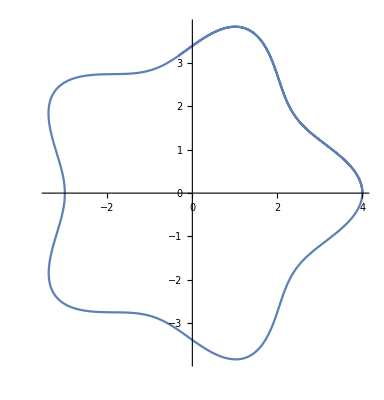

```mathematica
R[t_] := Sqrt[9Sin[t]^2+16Cos[t]^2];
T[t_] := NIntegrate[1/R[a]^2, {a, 0, t}];
X[t_] := R[t]Cos[4.802T[t]];
Y[t_] := R[t]Sin[4.802T[t]];
ParametricPlot[{X[t], Y[t]}, {t, 0, 20}]
```